1. Use of ListPlot to display the random numbers
2. Use of Histogram to display the distribution
3. Use of a gaussian model and FindFit to fit the histogram

```mathematica
Remove["Global`*"]
data= Import["~/Github/math_on_a_comp/RandomNumbers.dat.txt","Table"][[All,1]]
```

{5.56526,4.89033,2.83578,4.42995,4.00977,5.16808,5.0737,4.84722,5.61556,4.3286,4.99025,4.62328,5.50225,6.08607,5.06127,5.35189,4.20011,4.22681,4.56419,6.10998,7.02263,4.84943,5.52205,3.45016,2.92722,5.56329,4.15545,3.7403,4.75305,3.80469,3.41311,4.87647,4.39206,4.80639,6.9455,5.13443,4.62464,4.94683,5.32573,3.46884,4.04768,3.96748,5.32515,4.76426,3.86146,3.49761,4.56432,5.81766,4.60426,6.46068,5.23597,4.56854,3.49587,4.1186,5.03874,4.30412,5.20945,3.09228,2.74368,3.90086,5.28223,5.11369,5.68495,4.21278,3.81071,3.63603,4.85338,4.74958,6.04126,3.72008,5.12467,5.82153,3.72043,4.28536,3.81249,5.5682,4.55116,4.57583,6.16103,5.23445,5.5969,4.42702,5.57282,3.73981,4.05927,5.27925,5.00526,4.49048,4.02842,4.72165,4.81155,5.45087,5.10945,4.43549,3.8027,4.41461,7.08328,4.54686,5.15475,5.1565,6.18993,4.10472,5.45416,5.68641,5.40507,5.31681,4.88304,4.84416,5.26418,5.25819,4.96147,4.59427,3.34621,4.41017,5.25314,4.03841,6.10612,6.55087,6.37706,5.97856,5.45593,5.51944,7.26746,4.89981,6.30838,6.0515,4.66512,3.92273,3.05318,4.82149,2.26823,4.86539,4.96124,5.43803,5.17637,5.02054,6.46811,3.78541,6.517,5.16065,4.05907,5.26752,4.71161,4.0898,3.79325,3.51588,5.87501,5.64772,3.73052,4.7638,4.99037,4.71335,4.08683,4.91998,5.83423,5.11583,5.1817,3.17429,4.69437,4.48881,4.41667,5.39372,4.9574,4.85741,6.00897,4.84382,4.49049,5.18541,4.02076,4.38299,5.35838,5.11503,5.28874,4.24273,4.37422,5.17567,4.49348,3.39988,4.21343,4.45951,6.23008,5.2795,4.77013,5.102,6.64157,5.74318,4.02915,7.15337,3.90286,6.41818,4.56273,4.99947,5.77899,4.81951,6.16411,4.55686,4.74773,6.58948,6.58623,6.02577,7.06164,5.16321,4.03702,4.70137,4.94952,3.90214,6.29478,3.67114,6.23714,4.95738,6.06625,4.85063,7.60605,4.27204,3.96909,3.616,2.77473,4.98713,5.60852,6.27729,4.98032,4.78374,4.28438,6.38542,4.58318,4.95743,5.95003,3.45722,4.77121,5.14936,3.42891,4.59866,5.12075,4.00678,4.91813,4.86451,4.53212,5.33931,5.70859,4.80086,3.8882,5.23584,6.21274,5.14123,5.52387,5.24976,4.03246,5.24397,5.27886,5.35726}

```mathematica
Length[data]
Max[data]
Min[data]
Dimensions[data]
N[Mean[data]]
N[Median[data]]
```

250

7.60605

2.26823

{250}

4.89815

4.88669

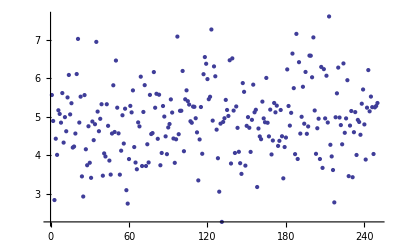

```mathematica
ListPlot[data]
```

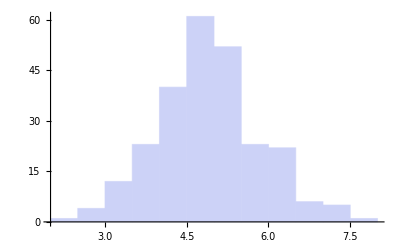

```mathematica
Histogram[data]
```

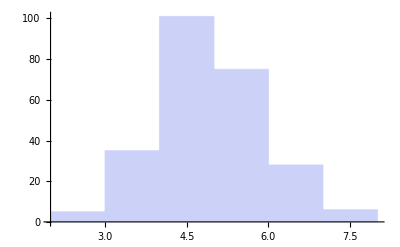

```mathematica
Histogram[data,{{2,3,4,5,6,7,8}}]
```

```mathematica
BinCounts[data]
```

{5,35,101,75,28,6}

```mathematica
BinCounts[Flatten[data],{0,10,.5}]
```

{0,0,0,0,1,4,12,23,40,61,52,23,22,6,5,1,0,0,0,0}

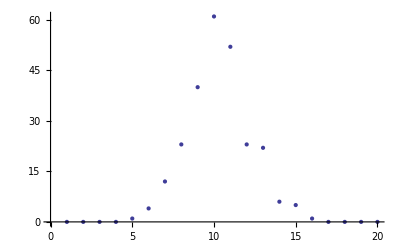

```mathematica
ListPlot[BinCounts[Flatten[data],{0,10,.5}]]
```

a ⅇ^(-(b+x)^2/(2 c^2))

{a→56.2848,b→-10.2035,c→1.70589}

Function[{x},56.2848 ⅇ^(-0.171817 (-10.2035+x)^2)]

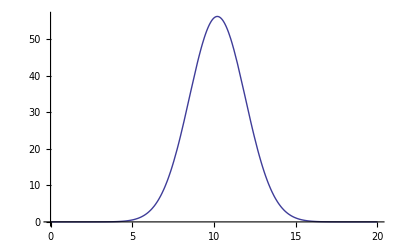

```mathematica
model = a*Exp[-(b+x)^2/(2*c^2)]
fitParams = FindFit[BinCounts[Flatten[data],{0,10,.5}],{model},{a,b,c},x]
modelFit = Function[{x},Evaluate[model/.fitParams]]
Plot[modelFit[x],{x,0,20}]
```

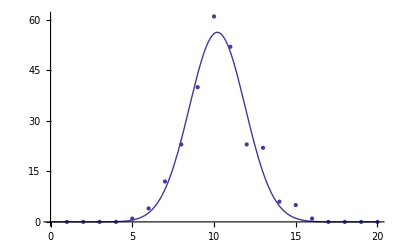

```mathematica
Show[ListPlot[BinCounts[Flatten[data],{0,10,.5}]], Plot[modelFit[x],{x,0,20}]]
```

Determination of half-life using
1. an exponential model
2. a linear model in log-scale

As mentioned in class, there is a certain level of noise added by the Cesium decay process.
I assumed that the data points after time = 60 (in units of 20 secs) to be completely noise and I subtracted the whole data set using a mean of the data points between 60 and 100.
I then proceeded to fit only the first 38 data points in the cleaned data set as the 39th data point is negative, which cannot be modeled given an exponential form.

```mathematica
Remove["Global`*"]
```

```mathematica
rawData = Import["~/Github/math_on_a_comp/Cs137.dat.txt","Table"]
```

{{0,283},{1,249},{2,209},{3,239},{4,216},{5,203},{6,185},{7,165},{8,148},{9,127},{10,123},{11,131},{12,99},{13,98},{14,90},{15,90},{16,88},{17,59},{18,55},{19,52},{20,56},{21,76},{22,46},{23,43},{24,43},{25,36},{26,43},{27,37},{28,33},{29,37},{30,24},{31,42},{32,27},{33,34},{34,25},{35,22},{36,29},{37,23},{39,10},{40,17},{41,12},{42,19},{43,16},{44,13},{45,16},{46,13},{47,18},{48,7},{49,12},{50,19},{51,18},{52,12},{53,15},{54,11},{55,8},{56,12},{57,9},{58,14},{59,16},{60,12},{61,12},{62,8},{63,9},{64,10},{65,14},{66,10},{67,10},{68,14},{69,6},{70,11},{71,13},{72,14},{73,11},{74,12},{75,8},{76,12},{77,15},{78,6},{79,15},{80,10},{81,10},{82,10},{83,10},{84,12},{85,4},{86,7},{87,9},{88,9},{89,15},{90,9},{91,13},{92,7},{93,12},{94,7},{95,13},{96,11},{97,14},{98,14},{99,11},{100,11}}

```mathematica
N[Mean[rawData[[60;;100,2]]]]
```

10.7317

```mathematica
cleanData = rawData[[All,2]]-N[Mean[rawData[[60;;100,2]]]]
```

{272.268,238.268,198.268,228.268,205.268,192.268,174.268,154.268,137.268,116.268,112.268,120.268,88.2683,87.2683,79.2683,79.2683,77.2683,48.2683,44.2683,41.2683,45.2683,65.2683,35.2683,32.2683,32.2683,25.2683,32.2683,26.2683,22.2683,26.2683,13.2683,31.2683,16.2683,23.2683,14.2683,11.2683,18.2683,12.2683,-0.731707,6.26829,1.26829,8.26829,5.26829,2.26829,5.26829,2.26829,7.26829,-3.73171,1.26829,8.26829,7.26829,1.26829,4.26829,0.268293,-2.73171,1.26829,-1.73171,3.26829,5.26829,1.26829,1.26829,-2.73171,-1.73171,-0.731707,3.26829,-0.731707,-0.731707,3.26829,-4.73171,0.268293,2.26829,3.26829,0.268293,1.26829,-2.73171,1.26829,4.26829,-4.73171,4.26829,-0.731707,-0.731707,-0.731707,-0.731707,1.26829,-6.73171,-3.73171,-1.73171,-1.73171,4.26829,-1.73171,2.26829,-3.73171,1.26829,-3.73171,2.26829,0.268293,3.26829,3.26829,0.268293,0.268293}

```mathematica
cleanData[[39]]
```

-0.731707

```mathematica
Length[cleanData]
Max[cleanData]
Min[cleanData]
Dimensions[cleanData]
N[Mean[cleanData]]
N[Median[cleanData]]
```

100

272.268

-6.73171

{100}

32.3883

3.76829

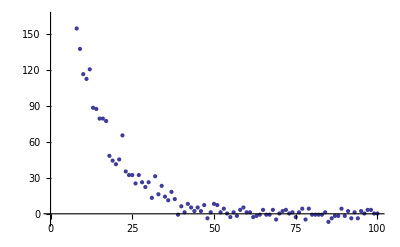

```mathematica
ListPlot[cleanData]
```

a ⅇ^(-b t)

{a→295.302,b→0.0854719}

Function[{t},295.302 ⅇ^(-0.0854719 t)]

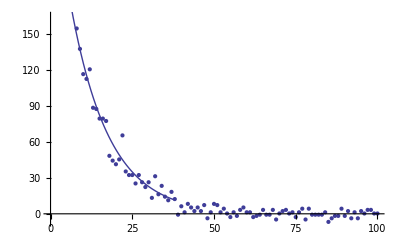

```mathematica
model = a*Exp[-b*t]
fitParams = FindFit[cleanData[[1;;38]],{model},{a,b},t]
modelFit = Function[{t},Evaluate[model/.fitParams]]
Show[ListPlot[cleanData], Plot[modelFit[t],{t,0,38}]]
```

estimate of half life using exponential fit

```mathematica
N[1/0.08547187895500148/3]
```

3.89992

{295.302,271.111,248.901,228.511,209.791,192.605,176.826,162.341,149.041,136.832,125.622,115.331,105.883,97.2092,89.2457,81.9346,75.2224,69.0601,63.4026,58.2086,53.4401,49.0622,45.043,41.353,37.9654,34.8552,31.9998,29.3784,26.9717,24.7621,22.7336,20.8712,19.1614,17.5917,16.1506,14.8275,13.6128,12.4976}

{-23.0339,-32.8425,-50.6328,-0.242563,-4.52272,-0.336419,-2.55804,-8.07224,-11.7731,-20.5635,-13.3541,4.93701,-17.6149,-9.94087,-9.97739,-2.66629,2.04588,-20.7918,-19.1343,-16.9403,-8.17183,16.206,-9.77473,-9.08476,-5.69707,-9.58691,0.268465,-3.11008,-4.70337,1.50618,-9.46528,10.3971,-2.89313,5.67659,-1.88228,-3.55921,4.65548,-0.229347}

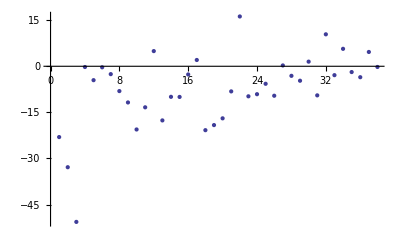

```mathematica
dataFit =Table[modelFit[t],{t,0,37}]
diff = cleanData[[1;;38]] - dataFit
ListPlot[diff]
```

a-b t

{a→5.64975,b→0.0839237}

Function[{t},5.64975-0.0839237 t]

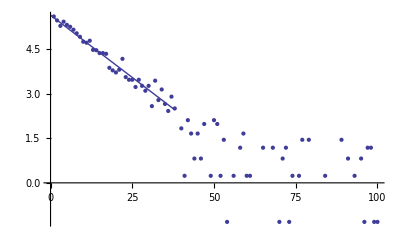

```mathematica
model = a - b*t
fitParams = FindFit[N[Log[cleanData[[1;;38]]]],{model},{a,b},t]
modelFit = Function[{t},Evaluate[model/.fitParams]]
Show[ListPlot[Log[cleanData]], Plot[modelFit[t],{t,0,38}]]
```

estimate of half life using log-linear fit

```mathematica
N[1/0.08392370337002768/3]
```

3.97186

{10.9271,-2.03526,-22.6912,25.0958,18.4509,20.4894,16.3174,9.03219,3.72349,-6.52634,-0.641545,16.4475,-7.19504,-0.510374,-1.44431,5.05294,9.02717,-14.4795,-13.4284,-11.7839,-3.51328,20.4136,-5.97569,-5.6556,-2.60278,-6.79571,2.7854,-0.841273,-2.65899,3.34762,-7.8073,11.8893,-1.55076,6.88365,-0.797409,-2.58464,5.5305,0.555875}

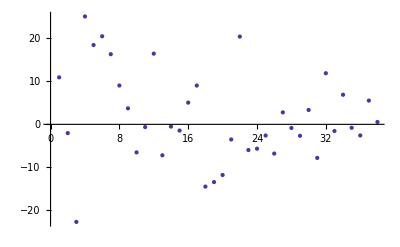

```mathematica
diffLogFit =cleanData[[1;;38]] -Exp[Table[modelFit[t],{t,1,38}]]
ListPlot[diffLogFit]
```

If the data fitting is done without cleaning the data i.e subtracting the noise level,
the following analysis holds.

```mathematica
Remove["Global`*"]
dataToFit = Import["~/Github/math_on_a_comp/Cs137.dat.txt","Table"]
```

{{0,283},{1,249},{2,209},{3,239},{4,216},{5,203},{6,185},{7,165},{8,148},{9,127},{10,123},{11,131},{12,99},{13,98},{14,90},{15,90},{16,88},{17,59},{18,55},{19,52},{20,56},{21,76},{22,46},{23,43},{24,43},{25,36},{26,43},{27,37},{28,33},{29,37},{30,24},{31,42},{32,27},{33,34},{34,25},{35,22},{36,29},{37,23},{39,10},{40,17},{41,12},{42,19},{43,16},{44,13},{45,16},{46,13},{47,18},{48,7},{49,12},{50,19},{51,18},{52,12},{53,15},{54,11},{55,8},{56,12},{57,9},{58,14},{59,16},{60,12},{61,12},{62,8},{63,9},{64,10},{65,14},{66,10},{67,10},{68,14},{69,6},{70,11},{71,13},{72,14},{73,11},{74,12},{75,8},{76,12},{77,15},{78,6},{79,15},{80,10},{81,10},{82,10},{83,10},{84,12},{85,4},{86,7},{87,9},{88,9},{89,15},{90,9},{91,13},{92,7},{93,12},{94,7},{95,13},{96,11},{97,14},{98,14},{99,11},{100,11}}

```mathematica
Length[dataToFit]
Max[dataToFit]
Min[dataToFit]
Dimensions[dataToFit]
N[Mean[dataToFit]]
N[Median[dataToFit]]
```

100

283

0

{100,2}

{50.12,43.12}

{50.5,14.5}

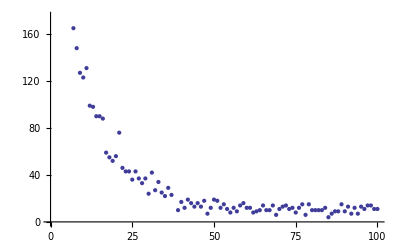

```mathematica
ListPlot[dataToFit]
```

a ⅇ^(-b t)

{a→272.771,b→0.0736178}

Function[{t},272.771 ⅇ^(-0.0736178 t)]

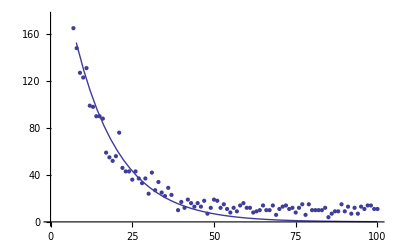

```mathematica
model = a*Exp[-b*t]
fitParams = FindFit[dataToFit,{model},{a,b},t]
modelFit = Function[{t},Evaluate[model/.fitParams]]
Show[ListPlot[dataToFit], Plot[modelFit[t],{t,0,100}]]
```

estimate of half life using exponential fit

```mathematica
N[1/0.07361778851033923/3]
```

4.52789

{253.412,235.426,218.717,203.194,188.773,175.375,162.928,151.365,140.622,130.641,121.369,112.755,104.753,97.318,90.411,83.9943,78.0329,72.4947,67.3495,62.5695,58.1287,54.0031,50.1703,46.6096,43.3016,40.2283,37.3732,34.7207,32.2564,29.9671,27.8402,25.8643,24.0286,22.3232,20.7389,19.267,17.8995,16.6292,15.4489,14.3525,13.3338,12.3875,11.5083,10.6915,9.9327,9.22775,8.57282,7.96438,7.39912,6.87398,6.38611,5.93287,5.5118,5.1206,4.75718,4.41955,4.10588,3.81447,3.54374,3.29223,3.05857,2.84149,2.63982,2.45247,2.27841,2.1167,1.96647,1.82691,1.69724,1.57679,1.46488,1.36091,1.26432,1.17459,1.09122,1.01378,0.941824,0.87498,0.81288,0.755187,0.701589,0.651795,0.605535,0.562558,0.522631,0.485539,0.451078,0.419064,0.389321,0.36169,0.33602,0.312171,0.290015,0.269432,0.25031,0.232544,0.21604,0.200707,0.186462,0.173228}

{29.5883,13.5738,-9.71725,35.8058,27.2272,27.625,22.072,13.6355,7.37833,-3.64129,1.63076,18.2447,-5.75266,0.681984,-0.411036,6.00573,9.96708,-13.4947,-12.3495,-10.5695,-2.12871,21.9969,-4.17034,-3.60959,-0.301551,-4.2283,5.62684,2.27933,0.743573,7.03292,-3.84022,16.1357,2.97137,11.6768,4.26111,2.73302,11.1005,6.37085,-5.44892,2.64754,-1.33382,6.61252,4.4917,2.30848,6.0673,3.77225,9.42718,-0.964382,4.60088,12.126,11.6139,6.06713,9.4882,5.8794,3.24282,7.58045,4.89412,10.1855,12.4563,8.70777,8.94143,5.15851,6.36018,7.54753,11.7216,7.8833,8.03353,12.1731,4.30276,9.42321,11.5351,12.6391,9.73568,10.8254,6.90878,10.9862,14.0582,5.12502,14.1871,9.24481,9.29841,9.34821,9.39447,11.4374,3.47737,6.51446,8.54892,8.58094,14.6107,8.63831,12.664,6.68783,11.71,6.73057,12.7497,10.7675,13.784,13.7993,10.8135,10.8268}

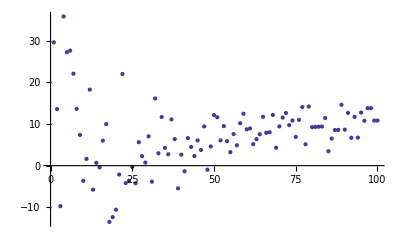

```mathematica
dataFit =Table[modelFit[t],{t,1,100}]
diff = dataToFit[[All,2]] - dataFit
ListPlot[diff]
```

a-b t

{a→4.68167,b→0.0310258}

Function[{t},4.68167-0.0310258 t]

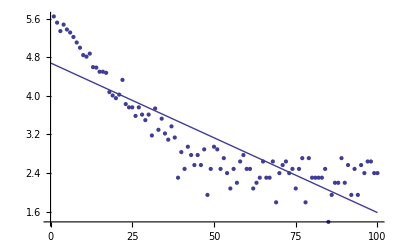

```mathematica
model = a - b*t
fitParams = FindFit[N[Log[dataToFit[[All,2]]]],{model},{a,b},t]
modelFit = Function[{t},Evaluate[model/.fitParams]]
Show[ListPlot[Log[dataToFit[[All,2]]]], Plot[modelFit[t],{t,0,100}]]
```

estimate of half life using log-linear fit

```mathematica
N[1/0.031025819073912657/3]
```

10.7437

{0.994807,0.897839,0.753746,0.918901,0.848742,0.817695,0.755871,0.672487,0.594779,0.47278,0.471803,0.565842,0.31679,0.337664,0.283532,0.314557,0.32311,-0.0456632,-0.0848416,-0.109905,-0.0047715,0.331636,-0.13943,-0.175846,-0.14482,-0.291475,-0.0827682,-0.202025,-0.285409,-0.139973,-0.541811,0.0488304,-0.361977,-0.100427,-0.376886,-0.473693,-0.166414,-0.36719,-1.16907,-0.607419,-0.9247,-0.434142,-0.574966,-0.75158,-0.512915,-0.689528,-0.33308,-1.24652,-0.676494,-0.185935,-0.208977,-0.583416,-0.329247,-0.608376,-0.895804,-0.459313,-0.715969,-0.243111,-0.0785533,-0.33521,-0.304184,-0.678623,-0.529814,-0.393428,-0.0259298,-0.331376,-0.30035,0.0671476,-0.749124,-0.111963,0.0861171,0.191251,-0.0188853,0.0991519,-0.275287,0.161204,0.415373,-0.469892,0.477425,0.102985,0.134011,0.165037,0.196063,0.40941,-0.658176,-0.0675348,0.214805,0.245831,0.787683,0.307883,0.706633,0.11862,0.688642,0.180672,0.830737,0.694709,0.966896,0.997922,0.787786,0.818812}

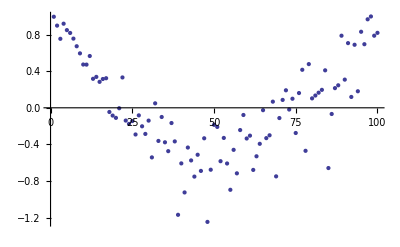

```mathematica
diffLogFit =Log[dataToFit[[All,2]]] -Table[modelFit[t],{t,1,100}]
ListPlot[diffLogFit]
```

{178.348,147.545,110.645,143.649,123.562,113.386,98.1238,80.7778,66.3507,47.8451,46.2632,56.6075,26.8801,28.0833,22.2193,24.2899,24.2973,-2.75659,-4.86996,-6.04096,-0.267843,21.4511,-6.88245,-8.26692,-6.70074,-12.1824,-3.71047,-8.28349,-10.9001,-5.55898,-17.2588,2.00161,-11.7765,-3.59186,-11.4434,-13.3301,-5.25081,-10.2045,-22.1901,-14.2067,-18.2533,-10.3291,-12.4331,-14.5645,-10.7224,-12.9061,-7.11466,-17.3474,-11.6036,-3.88255,-4.1835,-9.5058,-5.84881,-9.21189,-11.5944,-6.99583,-9.41552,-3.85293,-1.30754,-4.7788,-4.26622,-7.76929,-6.28755,-4.82052,-0.367765,-3.92884,-3.50332,0.9092,-6.69088,-1.30318,1.07267,2.43705,-0.209713,1.13274,-2.53527,1.78657,5.09859,-3.59893,5.69431,0.978597,1.2542,1.52138,1.78039,4.0315,-3.72507,-0.489072,1.73971,1.96151,8.17653,2.38499,6.58707,0.782984,5.97291,1.15703,7.33553,5.50858,8.67634,8.83898,5.99664,6.14949}

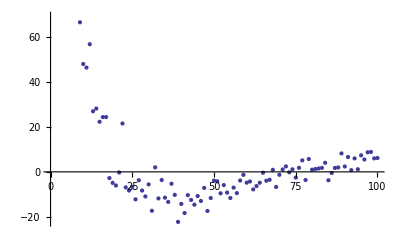

```mathematica
diffFit = dataToFit[[All,2]] -Exp[Table[modelFit[t],{t,1,100}]]
ListPlot[diffFit]
```